## Uppgift 4

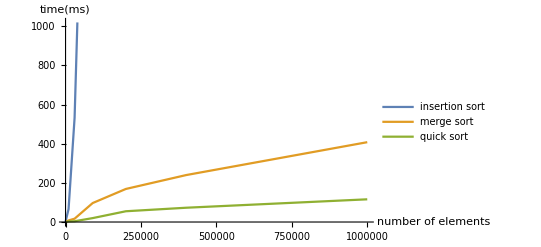

```mathematica
insertSortTimes = {{100,0},{1000,8},{10000,66},{30000,533},{90000,3705},{200000,18079}};
mergeSortTimes = {{100,0},{1000,1},{10000,8},{30000,17},{90000,97},{200000,169},{400000,240},{1000000,408}};
quickSortTimes = {{100,0},{1000,0},{10000,3},{30000,4},{90000,20},{200000,55},{400000,73},{1000000,116}};
ListLinePlot[{insertSortTimes,mergeSortTimes,quickSortTimes}, AxesLabel->{"number of elements", "time(ms)"}, PlotLegends->{"insertion sort", "merge sort", "quick sort"}]
```

## DISCUSSION:

We see clearly that insertion sort take exponentially more time when increasing the amount of elements to be sorted. We see that both merge sort and quick sort grows in a logarithmic pattern, with quick sort growing remarkably slower.

*Insertion sort is obviously the slowest sorting algorithm of the three tested, but the algorithm is also simpler to understand/implement making it a solid choice of sorting algorithm if handling small amounts of data.

*Merge sort definitely has its advantage over insertion sort when comparing speed. However, if falls short when compared to quick sort, being faster in all scenarios of this lab.

*Quick sort is the clear winner in this lab, it is a really fast sorting algorithm that can sort a large amount of data within reasonable time. The only possible con is that it is a bit more complex to understand and more difficult to implement, which might make it less neccesary if working with small amounts of data.